```mathematica
Quit[]
```

## Tools FG

```mathematica
(*cl[d_,l_]:=(Sqrt[π]Gamma[l+1]Gamma[(d-2)/2])/(2^(l+1) Gamma[l+(d-1)/2]);(*some other normalization term*)(*d-dim Partial Wave integrand {t,4,∞}*)*)
```

```mathematica
Clear[PolQ, PolQDer, z0t,z0u,tt,uu,discZ];
PolQ[J_, d_, z_]:=(4/Pi)(Sqrt[Pi]Gamma[J+1]Gamma[(d-2)/2])/(2^(J+1)Gamma[J+(d-1)/2] z^(J+1))Hypergeometric2F1[(J+1)/2,(J+2)/2, J+(d-1)/2,1/z^2];
PolQDer[J_,d_,z_]:=(D[PolQ[J,d,zz],{zz,1}]/.zz->z);
z0t[s_]:= (s+4)/(s-4);
z0u[s_]:= (s+4)/(4-s);
tt[s_,z_]:=((4-s)/2) (1-z);
uu[s_,z_]:=((4-s)/2 )(1+z);
discZ[expr_,s_,z_,eps_:10^-12]:= (expr[Re[s],z+eps I]-expr[Re[s],z-eps I])/(2I)
```

```mathematica
Clear[iQInfinity12,tail]
iQInfinity12[start_, J_, d_]=Integrate[PolQ[J,d,z] 1/z^(1/2), {z, start, Infinity}, GenerateConditions->False]
tail[amplitudeT_, s_, J_, d_, start_]:= Module[{zvals, yvals, coeff12},
								zvals = Abs[start[s]]*{100000,1000000, 10000000};
								yvals=amplitudeT[s,#]&/@zvals;
								coeff12=Mean[yvals*zvals^(1/2)];
								iQInfinity12[50000Abs[start[s]], J, d]coeff12]
```

1/(√π)2^-J (1/start^2)^(1/4+J/2) Gamma[-1+d/2] Gamma[1/4+J/2] Gamma[1+J] HypergeometricPFQRegularized[{1/4 (1+2 J),(1+J)/2,(2+J)/2},{1/4 (5+2 J),1/2 (-1+d)+J},1/start^2]

```mathematica
Clear[MyNIntegrateFaster];
MyNIntegrateFaster[expr_,{x_,a_,b_},p_]:=Module[{temp=expr},(*Print["integrate..."];*)temp=SetPrecision[temp,8*p];
temp=NIntegrate[temp,{x,a,b},Method->"GaussKronrodRule",WorkingPrecision->4*p,PrecisionGoal->p,AccuracyGoal->p,MaxRecursion->100];
temp=SetPrecision[temp,p];
Return[temp];];
```

```mathematica
Clear[t,u, rho, rhoT,rhoZ]
rho[s_,sigma_:20/3]:=(Sqrt[sigma-4]-Sqrt[4-s])/(Sqrt[sigma-4]+Sqrt[4-s])
rhoZ[s_,z_]:=rho[tt[s,z]];
(*Discontinuity of the rho wavelet*)
rhoT[t_,sigma_:20/3]:=(2 Sqrt[t-4] Sqrt[sigma-4])/(t+sigma-8)
```

## Comparison Froissart Gribov and usual projection for rho ansatz s>4

```mathematica
d=4;
```

```mathematica
Clear[exprSTU,expr,DiscExpr]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExpr[s_,z_]:=rhoT[tt[s,z]]
```

```mathematica
Clear[exprJmain,exprJtail,exprJ]
p0=8;
exprJmain[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z](*exprInt[z]*)DiscExpr[s,z],{z, z0t[s],(*50000 z0[s]*)Infinity},p0];
exprJtail[J_,s_]=tail[DiscExpr, s, J, d,z0t];
exprJ[J_,s_]:=exprJmain[J,s]+exprJtail[J,s];
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
data4ds5to95=ParallelTable[{J,Abs[(exprJmain[J,s+10^-16 I]-IPt[J,s+10^-16 I])/(exprJmain[J,s+10^-16 I]+IPt[J,s+10^-16 I])]},{s,5,95,10},{J,2,12,2}]
```

{{{2,2.×10^-7},{4,1.3×10^-6},{6,2.×10^-6},{8,2.9×10^-6},{10,3.84×10^-6},{12,4.92×10^-6}},{{2,0.},{4,0.},{6,4.58×10^-6},{8,0.00005191},{10,0.0000686},{12,0.00008669}},{{2,0.},{4,0.},{6,0.},{8,4.39×10^-6},{10,0.00004617},{12,0.0001647}},{{2,0.},{4,0.},{6,0.},{8,2.3×10^-6},{10,8.37×10^-6},{12,0.0000296}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,3.85×10^-6},{12,0.0000136}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,5.87×10^-6}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,6.93×10^-6}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}}}

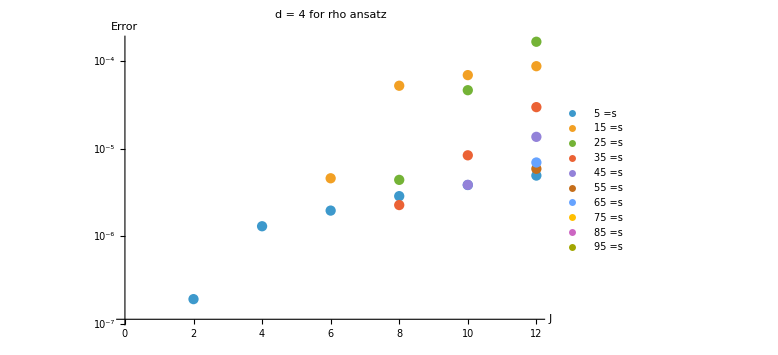

```mathematica
ListLogPlot[data4ds5to95,PlotLabel->Style["d = 4 for rho ansatz",16,Bold],AxesLabel->{Style["J",14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

## Comparison Froissart Gribov and usual projection for rho ansatz s<4

```mathematica
Clear[exprSTU,expr,DiscExpr]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExpr[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[exprJmain,exprJtail,exprJ]
p0=8;
exprJmain[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z](*exprInt[z]*)DiscExpr[s,z],{z, z0u[s],(*50000 Abs[z0u[s]]*)Infinity},p0];
(*exprJtail[J_,s_]=iQInfinity12[50000 Abs[z0u[s]], J, d](Series[DiscExpr[-10+10^-10 I,z],{z,Infinity,1}]Sqrt[z]//Normal)/.z->1;
exprJ[J_,s_]:=exprJmain[J,s]+exprJtail[J,s];*)
```

```mathematica
MyNIntegrateFaster[PolQ[6,d,z](*exprInt[z]*)DiscExpr[-10-10^-10 I,z],{z, z0u[-10-10^-10 I],(*50000 z0[s]*)1},p0]
MyNIntegrateFaster[PolQ[6,d,z](*exprInt[z]*)DiscExpr[-10+10^-10 I,z],{z, z0u[-10+10^-10 I],(*50000 z0[s]*)1},p0]
exprJmain[6,-10+10^-10 I]
IPt[6,-10+10^-10 I]
```

0.04223488-0.053347348 ⅈ

0.04223488+0.053347348 ⅈ

0.066715075+0.05334734 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.06671507707308969+0.053347347900037 ⅈ

```mathematica
data4dsmin10to2=ParallelTable[{J,Quiet[Abs[(exprJmain[J,s-10^-16 I]-IPt[J,s-10^-16 I])/(exprJmain[J,s-10^-16 I]+IPt[J,s-10^-16 I])]]},{s,-10,2,2},{J,2,12,2}];
```

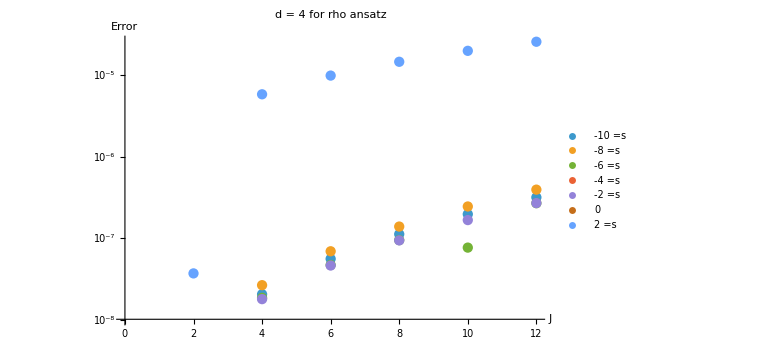

```mathematica
ListLogPlot[data4dsmin10to2,PlotLabel->Style["d = 4 for rho ansatz",16,Bold],AxesLabel->{Style["J",14],Style["Error",14]},PlotLegends->"=s"Range[-10,2,2],ImageSize->Large]
```

## Computation rho ansatz deep s

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=rhoT[tt[s,z]]
DiscExprU[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[exprJmain1,exprJmain2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z]DiscExprT[s,z],{z, z0t[s],Infinity},p0];
exprJmain2[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z]DiscExprU[s,z],{z, z0u[s],Infinity},p0];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s],exprJmain2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
exprJ[2,-10-9I ]-IPt[2,-10-9I ]
```

0.+0. ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Following the cuts

```mathematica
z1[s_,t_]:=1+(2t)/(s-4);
```

```mathematica
b0 = Table[z1[4+Exp[I Pi theta],t],{theta,0,1,0.1},{t,4,100,0.1}];(*
a0 = Table[z0t[4+Exp[2I Pi theta+I 0.01]]+t Exp[I Arg[z0t[4+Exp[2I Pi theta]]-1]],{theta,0,1,0.1},{t,0,100,1}];*)
```

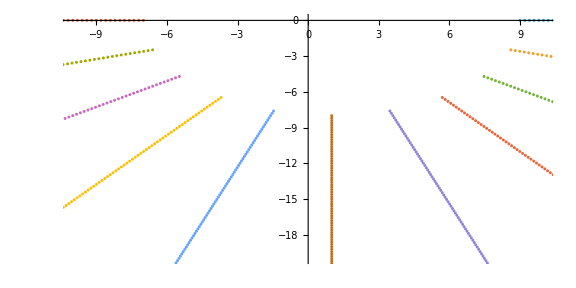

```mathematica
Show[ComplexListPlot[b0, ImageSize->Large, PlotRange->{-20-20I,20+0.1I}, AspectRatio->1/2](*,ComplexListPlot[a0, ImageSize->Large, PlotRange->{-10-20I,10+20I}, AspectRatio->1]*)]
```

## Computation rho ansatz deep s domain int compactified

The relatively low precision of half infinite domain and the hardship of looking at the tail on an angled branch cut means compactifying the integral might be the most effective pass.

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=rhoT[tt[s,z]]
DiscExprU[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[HalfCompactify,CompactIntegrand]
HalfCompactify[s0_,ϕ_]:=(2 s0)/(1+Cos[ϕ]);
CompactIntegrand[x_,var_,s0_]:=D[HalfCompactify[s0,ϕ],ϕ] (x/.var->HalfCompactify[s0,ϕ]);
```

```mathematica
Clear[exprJmain1,exprJmain2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprT[s,z])//CompactIntegrand[#,z,z0t[s]]&,{ϕ,0,π},p0];
exprJmain2[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprU[s,z])//CompactIntegrand[#,z,z0u[s]]&,{ϕ,0,π},p0];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s],exprJmain2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},p0]
```

```mathematica
exprJ[2,-10-9I ]-IPt[2,-10-9I ]
```

0.+0. ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Computation divergent threshold (n half integer) deep s domain int compactified d=6

```mathematica
d=6;
n=0;
div[s_]:=(4-s)^(-n-1/2)
divT[s_]:=(-1)^n(s-4)^(-n-1/2)
```

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=div[s]+div[u]+div[t];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=divT[tt[s,z]]
DiscExprU[s_,z_]:=divT[uu[s,z]]
```

```mathematica
Clear[epsilonT,epsilonU]
epsilonT[J_,s_]=(*Abs[PolQ[J, d, z0t[s]]/PolQDer[J,d,z0t[s],1]]*)10^-5//Simplify;
epsilonU[J_,s_]=(*Abs[PolQ[J, d, z0u[s]]/PolQDer[J,d,z0u[s],1]]*)10^-5//Simplify;
```

Might be optimized by precomputing the derivatives to the Legendre Q function.

```mathematica
Clear[HalfCompactify,CompactIntegrand]
HalfCompactify[s0_,ϕ_]:=(2 s0)/(1+Cos[ϕ]);
CompactIntegrand[x_,var_,s0_]:=D[HalfCompactify[s0,ϕ],ϕ] (x/.var->HalfCompactify[s0,ϕ]);
```

```mathematica
Clear[exprJmain1,exprJmain2,exprJkeyhole1,exprJkeyhole2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprT[s,z])//CompactIntegrand[#,z,z0t[s]+Exp[I Arg[-1+z0t[s]]]epsilonT[J,s]]&,{ϕ,0,π},p0];
exprJkeyhole1[J_, s_, ord_: 4] := Module[
  {z0, dir, eps, α, c0, qk},
  z0  = z0t[s];
  dir = Exp[I Arg[z0 - 1]];   (* direction of the cut / keyhole ray *)
  eps = epsilonT[J, s];
  α   = n + 1/2;
  (* regular prefactor of the discontinuity at the branch point *)
  c0 = Limit[
    (z - z0)^α DiscExprT[s, z],
    z -> z0,
    Direction -> dir
  ];
  qk[k_] := SeriesCoefficient[PolQ[J, d, z], {z, z0, k}];
  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
];
exprJmain2[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprU[s,z])//CompactIntegrand[#,z,z0u[s]+Exp[I Arg[1+z0u[s]]]epsilonU[J,s]]&,{ϕ,0,π},p0];
exprJkeyhole2[J_, s_, ord_: 4] := Module[
  {z0, dir, eps, α, c0, qk},
  z0  = z0u[s];
  dir = Exp[I Arg[z0 + 1]];   (* direction of the cut / keyhole ray *)
  eps = epsilonU[J, s];
  α   = n + 1/2;
  (* regular prefactor of the discontinuity at the branch point *)
  c0 = Limit[
    (z - z0)^α DiscExprT[s, z],
    z -> z0,
    Direction -> dir
  ];
  qk[k_] := SeriesCoefficient[PolQ[J, d, z], {z, z0, k}];
  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s]+exprJkeyhole1[J,s],exprJmain2[J,s]+exprJkeyhole2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
JJ=8;
ss=9+ 2I;
(exprJ[JJ,ss ]-IPt[JJ,ss  ])/(exprJ[JJ,ss ]+IPt[JJ,ss  ])
exprJ[JJ,ss ]
IPt[JJ,ss  ]
```

0.00094314+0.0000674 ⅈ

-1.324478×10^-8+3.8103212×10^-8 ⅈ

-1.32146940732641×10^-8+3.803318778346198×10^-8 ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,0.1,10.1,1}]]
```

{10.9055,{{{{-10.1,0.1,1.01491},{-10.1,1.1,1.01522},{-10.1,2.1,1.01549},{-10.1,3.1,1.01572},{-10.1,4.1,1.01592},{-10.1,5.1,1.01609},{-10.1,6.1,1.01624},{-10.1,7.1,1.01638},{-10.1,8.1,1.0165},{-10.1,9.1,1.01661},{-10.1,10.1,1.01671}},{{-9.1,0.1,1.01499},{-9.1,1.1,1.01532},{-9.1,2.1,1.01559},{-9.1,3.1,1.01582},{-9.1,4.1,1.01602},{-9.1,5.1,1.01618},{-9.1,6.1,1.01632},{-9.1,7.1,1.01644},{-9.1,8.1,1.01655},{-9.1,9.1,1.01666},{-9.1,10.1,1.01675}},{{-8.1,0.1,1.01509},{-8.1,1.1,1.01543},{-8.1,2.1,1.01571},{-8.1,3.1,1.01594},{-8.1,4.1,1.01612},{-8.1,5.1,1.01627},{-8.1,6.1,1.01639},{-8.1,7.1,1.0165},{-8.1,8.1,1.0166},{-8.1,9.1,1.01669},{-8.1,10.1,1.01678}},{{-7.1,0.1,1.0152},{-7.1,1.1,1.01557},{-7.1,2.1,1.01586},{-7.1,3.1,1.01607},{-7.1,4.1,1.01623},{-7.1,5.1,1.01635},{-7.1,6.1,1.01645},{-7.1,7.1,1.01654},{-7.1,8.1,1.01663},{-7.1,9.1,1.01671},{-7.1,10.1,1.0168}},{{-6.1,0.1,1.01536},{-6.1,1.1,1.01576},{-6.1,2.1,1.01603},{-6.1,3.1,1.01622},{-6.1,4.1,1.01634},{-6.1,5.1,1.01643},{-6.1,6.1,1.0165},{-6.1,7.1,1.01657},{-6.1,8.1,1.01664},{-6.1,9.1,1.01672},{-6.1,10.1,1.0168}},{{-5.1,0.1,1.01558},{-5.1,1.1,1.016},{-5.1,2.1,1.01625},{-5.1,3.1,1.01638},{-5.1,4.1,1.01644},{-5.1,5.1,1.01648},{-5.1,6.1,1.01652},{-5.1,7.1,1.01657},{-5.1,8.1,1.01662},{-5.1,9.1,1.01669},{-5.1,10.1,1.01678}},{{-4.1,0.1,1.01591},{-4.1,1.1,1.01634},{-4.1,2.1,1.01652},{-4.1,3.1,1.01655},{-4.1,4.1,1.01652},{-4.1,5.1,1.0165},{-4.1,6.1,1.01649},{-4.1,7.1,1.01652},{-4.1,8.1,1.01657},{-4.1,9.1,1.01664},{-4.1,10.1,1.01673}},{{-3.1,0.1,1.01645},{-3.1,1.1,1.01685},{-3.1,2.1,1.01684},{-3.1,3.1,1.01668},{-3.1,4.1,1.01653},{-3.1,5.1,1.01644},{-3.1,6.1,1.0164},{-3.1,7.1,1.01642},{-3.1,8.1,1.01648},{-3.1,9.1,1.01655},{-3.1,10.1,1.01665}},{{-2.1,0.1,1.01744},{-2.1,1.1,1.0176},{-2.1,2.1,1.01714},{-2.1,3.1,1.0167},{-2.1,4.1,1.01641},{-2.1,5.1,1.01627},{-2.1,6.1,1.01623},{-2.1,7.1,1.01626},{-2.1,8.1,1.01633},{-2.1,9.1,1.01643},{-2.1,10.1,1.01655}},{{-1.1,0.1,1.01974},{-1.1,1.1,1.01857},{-1.1,2.1,1.0172},{-1.1,3.1,1.01644},{-1.1,4.1,1.01608},{-1.1,5.1,1.01595},{-1.1,6.1,1.01594},{-1.1,7.1,1.01602},{-1.1,8.1,1.01613},{-1.1,9.1,1.01627},{-1.1,10.1,1.01642}},{{-0.1,0.1,1.02761},{-0.1,1.1,1.01845},{-0.1,2.1,1.01645},{-0.1,3.1,1.01571},{-0.1,4.1,1.01547},{-0.1,5.1,1.01546},{-0.1,6.1,1.01556},{-0.1,7.1,1.01571},{-0.1,8.1,1.01589},{-0.1,9.1,1.01608},{-0.1,10.1,1.01627}},{{0.9,0.1,1.01635},{0.9,1.1,1.01535},{0.9,2.1,1.01465},{0.9,3.1,1.01449},{0.9,4.1,1.01461},{0.9,5.1,1.01483},{0.9,6.1,1.0151},{0.9,7.1,1.01537},{0.9,8.1,1.01563},{0.9,9.1,1.01588},{0.9,10.1,1.01612}},{{1.9,0.1,1.0115},{1.9,1.1,1.01182},{1.9,2.1,1.01242},{1.9,3.1,1.01306},{1.9,4.1,1.01365},{1.9,5.1,1.01416},{1.9,6.1,1.01462},{1.9,7.1,1.01501},{1.9,8.1,1.01536},{1.9,9.1,1.01568},{1.9,10.1,1.01596}},{{2.9,0.1,1.00754},{2.9,1.1,1.00881},{2.9,2.1,1.01049},{2.9,3.1,1.01181},{2.9,4.1,1.0128},{2.9,5.1,1.01357},{2.9,6.1,1.01418},{2.9,7.1,1.01469},{2.9,8.1,1.01512},{2.9,9.1,1.0155},{2.9,10.1,1.01583}},{{3.9,0.1,1.0025},{3.9,1.1,1.00694},{3.9,2.1,1.00936},{3.9,3.1,1.01102},{3.9,4.1,1.01222},{3.9,5.1,1.01314},{3.9,6.1,1.01386},{3.9,7.1,1.01445},{3.9,8.1,1.01494},{3.9,9.1,1.01536},{3.9,10.1,1.01572}},{{4.9,0.1,1.64027×10^-9},{4.9,1.1,1.55014×10^-9},{4.9,2.1,5.33074×10^-10},{4.9,3.1,1.02011×10^-9},{4.9,4.1,1.95638×10^-9},{4.9,5.1,1.16132×10^-9},{4.9,6.1,9.51925×10^-10},{4.9,7.1,5.25678×10^-10},{4.9,8.1,5.78913×10^-10},{4.9,9.1,2.72328×10^-10},{4.9,10.1,7.24082×10^-10}},{{5.9,0.1,1.94465×10^-9},{5.9,1.1,2.24432×10^-9},{5.9,2.1,7.97234×10^-10},{5.9,3.1,1.32336×10^-9},{5.9,4.1,1.66272×10^-9},{5.9,5.1,1.66287×10^-9},{5.9,6.1,6.18726×10^-10},{5.9,7.1,2.0849×10^-10},{5.9,8.1,7.17821×10^-10},{5.9,9.1,1.21298×10^-10},{5.9,10.1,2.74131×10^-10}},{{6.9,0.1,5.06373×10^-11},{6.9,1.1,7.20153×10^-10},{6.9,2.1,3.13145×10^-10},{6.9,3.1,8.29134×10^-10},{6.9,4.1,6.48836×10^-10},{6.9,5.1,8.64855×10^-10},{6.9,6.1,1.03986×10^-9},{6.9,7.1,6.58386×10^-10},{6.9,8.1,6.45709×10^-10},{6.9,9.1,3.38835×10^-10},{6.9,10.1,6.69261×10^-10}},{{7.9,0.1,1.87075×10^-9},{7.9,1.1,2.27037×10^-9},{7.9,2.1,1.0887×10^-9},{7.9,3.1,1.2078×10^-9},{7.9,4.1,1.12688×10^-9},{7.9,5.1,4.54888×10^-10},{7.9,6.1,5.27577×10^-10},{7.9,7.1,7.38151×10^-10},{7.9,8.1,2.27059×10^-11},{7.9,9.1,1.73977×10^-10},{7.9,10.1,2.71396×10^-10}},{{8.9,0.1,1.5965×10^-9},{8.9,1.1,1.77296×10^-10},{8.9,2.1,8.49846×10^-11},{8.9,3.1,8.58309×10^-10},{8.9,4.1,8.69018×10^-10},{8.9,5.1,3.02074×10^-10},{8.9,6.1,2.31468×10^-10},{8.9,7.1,6.16965×10^-10},{8.9,8.1,8.33548×10^-10},{8.9,9.1,3.22418×10^-10},{8.9,10.1,6.42808×10^-10}},{{9.9,0.1,1.99653×10^-9},{9.9,1.1,8.46729×10^-10},{9.9,2.1,1.48765×10^-9},{9.9,3.1,8.59888×10^-10},{9.9,4.1,6.00318×10^-10},{9.9,5.1,3.17126×10^-10},{9.9,6.1,3.13207×10^-10},{9.9,7.1,2.30826×10^-10},{9.9,8.1,4.06879×10^-10},{9.9,9.1,1.93639×10^-10},{9.9,10.1,5.68858×10^-10}}},{{{-10.1,0.1,1.01938},{-10.1,1.1,1.0198},{-10.1,2.1,1.02018},{-10.1,3.1,1.02053},{-10.1,4.1,1.02083},{-10.1,5.1,1.02111},{-10.1,6.1,1.02135},{-10.1,7.1,1.02158},{-10.1,8.1,1.02179},{-10.1,9.1,1.02198},{-10.1,10.1,1.02217}},{{-9.1,0.1,1.01937},{-9.1,1.1,1.01982},{-9.1,2.1,1.02022},{-9.1,3.1,1.02058},{-9.1,4.1,1.02088},{-9.1,5.1,1.02115},{-9.1,6.1,1.02139},{-9.1,7.1,1.02161},{-9.1,8.1,1.02181},{-9.1,9.1,1.022},{-9.1,10.1,1.02218}},{{-8.1,0.1,1.01937},{-8.1,1.1,1.01986},{-8.1,2.1,1.02029},{-8.1,3.1,1.02064},{-8.1,4.1,1.02095},{-8.1,5.1,1.0212},{-8.1,6.1,1.02143},{-8.1,7.1,1.02163},{-8.1,8.1,1.02182},{-8.1,9.1,1.02201},{-8.1,10.1,1.02218}},{{-7.1,0.1,1.0194},{-7.1,1.1,1.01994},{-7.1,2.1,1.02038},{-7.1,3.1,1.02074},{-7.1,4.1,1.02102},{-7.1,5.1,1.02126},{-7.1,6.1,1.02146},{-7.1,7.1,1.02165},{-7.1,8.1,1.02183},{-7.1,9.1,1.022},{-7.1,10.1,1.02217}},{{-6.1,0.1,1.01947},{-6.1,1.1,1.02006},{-6.1,2.1,1.02052},{-6.1,3.1,1.02085},{-6.1,4.1,1.02111},{-6.1,5.1,1.02131},{-6.1,6.1,1.02149},{-6.1,7.1,1.02165},{-6.1,8.1,1.02181},{-6.1,9.1,1.02197},{-6.1,10.1,1.02214}},{{-5.1,0.1,1.01961},{-5.1,1.1,1.02026},{-5.1,2.1,1.02071},{-5.1,3.1,1.02101},{-5.1,4.1,1.0212},{-5.1,5.1,1.02135},{-5.1,6.1,1.02148},{-5.1,7.1,1.02162},{-5.1,8.1,1.02177},{-5.1,9.1,1.02193},{-5.1,10.1,1.02209}},{{-4.1,0.1,1.01987},{-4.1,1.1,1.0206},{-4.1,2.1,1.021},{-4.1,3.1,1.02118},{-4.1,4.1,1.02128},{-4.1,5.1,1.02135},{-4.1,6.1,1.02144},{-4.1,7.1,1.02155},{-4.1,8.1,1.02169},{-4.1,9.1,1.02185},{-4.1,10.1,1.02202}},{{-3.1,0.1,1.02037},{-3.1,1.1,1.02115},{-3.1,2.1,1.02138},{-3.1,3.1,1.02136},{-3.1,4.1,1.0213},{-3.1,5.1,1.02128},{-3.1,6.1,1.02133},{-3.1,7.1,1.02142},{-3.1,8.1,1.02156},{-3.1,9.1,1.02173},{-3.1,10.1,1.02191}},{{-2.1,0.1,1.02141},{-2.1,1.1,1.02208},{-2.1,2.1,1.02182},{-2.1,3.1,1.02143},{-2.1,4.1,1.02118},{-2.1,5.1,1.02109},{-2.1,6.1,1.02112},{-2.1,7.1,1.02122},{-2.1,8.1,1.02138},{-2.1,9.1,1.02157},{-2.1,10.1,1.02178}},{{-1.1,0.1,1.02406},{-1.1,1.1,1.02352},{-1.1,2.1,1.02205},{-1.1,3.1,1.0212},{-1.1,4.1,1.02082},{-1.1,5.1,1.02072},{-1.1,6.1,1.02078},{-1.1,7.1,1.02093},{-1.1,8.1,1.02114},{-1.1,9.1,1.02137},{-1.1,10.1,1.02162}},{{-0.1,0.1,1.03736},{-0.1,1.1,1.024},{-0.1,2.1,1.02134},{-0.1,3.1,1.02039},{-0.1,4.1,1.02011},{-0.1,5.1,1.02014},{-0.1,6.1,1.02032},{-0.1,7.1,1.02057},{-0.1,8.1,1.02085},{-0.1,9.1,1.02114},{-0.1,10.1,1.02144}},{{0.9,0.1,1.02182},{0.9,1.1,1.02024},{0.9,2.1,1.01916},{0.9,3.1,1.01892},{0.9,4.1,1.01907},{0.9,5.1,1.01938},{0.9,6.1,1.01976},{0.9,7.1,1.02014},{0.9,8.1,1.02053},{0.9,9.1,1.02089},{0.9,10.1,1.02125}},{{1.9,0.1,1.0152},{1.9,1.1,1.01557},{1.9,2.1,1.0163},{1.9,3.1,1.01711},{1.9,4.1,1.01787},{1.9,5.1,1.01856},{1.9,6.1,1.01916},{1.9,7.1,1.01971},{1.9,8.1,1.0202},{1.9,9.1,1.02065},{1.9,10.1,1.02106}},{{2.9,0.1,1.00993},{2.9,1.1,1.01159},{2.9,2.1,1.01378},{2.9,3.1,1.0155},{2.9,4.1,1.0168},{2.9,5.1,1.01781},{2.9,6.1,1.01863},{2.9,7.1,1.01932},{2.9,8.1,1.01992},{2.9,9.1,1.02044},{2.9,10.1,1.0209}},{{3.9,0.1,1.00328},{3.9,1.1,1.00913},{3.9,2.1,1.01231},{3.9,3.1,1.01448},{3.9,4.1,1.01607},{3.9,5.1,1.01728},{3.9,6.1,1.01824},{3.9,7.1,1.01903},{3.9,8.1,1.01969},{3.9,9.1,1.02027},{3.9,10.1,1.02077}},{{4.9,0.1,2.34559×10^-9},{4.9,1.1,1.79013×10^-9},{4.9,2.1,3.45084×10^-10},{4.9,3.1,7.71538×10^-10},{4.9,4.1,1.47819×10^-9},{4.9,5.1,8.73565×10^-10},{4.9,6.1,7.29707×10^-10},{4.9,7.1,4.01219×10^-10},{4.9,8.1,4.41752×10^-10},{4.9,9.1,2.07727×10^-10},{4.9,10.1,5.52117×10^-10}},{{5.9,0.1,1.52168×10^-9},{5.9,1.1,1.72687×10^-9},{5.9,2.1,8.97891×10^-10},{5.9,3.1,1.02714×10^-9},{5.9,4.1,1.26385×10^-9},{5.9,5.1,1.25698×10^-9},{5.9,6.1,4.82972×10^-10},{5.9,7.1,1.49117×10^-10},{5.9,8.1,5.46955×10^-10},{5.9,9.1,9.24247×10^-11},{5.9,10.1,2.08733×10^-10}},{{6.9,0.1,4.25499×10^-11},{6.9,1.1,6.17951×10^-10},{6.9,2.1,2.06537×10^-10},{6.9,3.1,6.43661×10^-10},{6.9,4.1,4.95557×10^-10},{6.9,5.1,6.50732×10^-10},{6.9,6.1,7.97184×10^-10},{6.9,7.1,4.9307×10^-10},{6.9,8.1,4.91342×10^-10},{6.9,9.1,2.57771×10^-10},{6.9,10.1,5.0897×10^-10}},{{7.9,0.1,1.47168×10^-9},{7.9,1.1,1.77372×10^-9},{7.9,2.1,8.6376×10^-10},{7.9,3.1,9.24947×10^-10},{7.9,4.1,8.49868×10^-10},{7.9,5.1,3.43838×10^-10},{7.9,6.1,4.03802×10^-10},{7.9,7.1,5.5814×10^-10},{7.9,8.1,1.72833×10^-11},{7.9,9.1,1.32246×10^-10},{7.9,10.1,2.06169×10^-10}},{{8.9,0.1,1.21918×10^-9},{8.9,1.1,1.07872×10^-10},{8.9,2.1,1.08624×10^-10},{8.9,3.1,6.54384×10^-10},{8.9,4.1,6.647×10^-10},{8.9,5.1,2.24352×10^-10},{8.9,6.1,1.70622×10^-10},{8.9,7.1,4.69824×10^-10},{8.9,8.1,6.32765×10^-10},{8.9,9.1,2.44704×10^-10},{8.9,10.1,4.8773×10^-10}},{{9.9,0.1,1.53716×10^-9},{9.9,1.1,6.71093×10^-10},{9.9,2.1,1.12724×10^-9},{9.9,3.1,6.50977×10^-10},{9.9,4.1,4.52606×10^-10},{9.9,5.1,2.37126×10^-10},{9.9,6.1,2.38575×10^-10},{9.9,7.1,1.75075×10^-10},{9.9,8.1,3.08528×10^-10},{9.9,9.1,1.46797×10^-10},{9.9,10.1,4.31172×10^-10}}},{{{-10.1,0.1,1.02292},{-10.1,1.1,1.02344},{-10.1,2.1,1.02392},{-10.1,3.1,1.02436},{-10.1,4.1,1.02475},{-10.1,5.1,1.02511},{-10.1,6.1,1.02544},{-10.1,7.1,1.02575},{-10.1,8.1,1.02603},{-10.1,9.1,1.0263},{-10.1,10.1,1.02655}},{{-9.1,0.1,1.02284},{-9.1,1.1,1.02341},{-9.1,2.1,1.02392},{-9.1,3.1,1.02437},{-9.1,4.1,1.02477},{-9.1,5.1,1.02513},{-9.1,6.1,1.02545},{-9.1,7.1,1.02575},{-9.1,8.1,1.02603},{-9.1,9.1,1.02629},{-9.1,10.1,1.02654}},{{-8.1,0.1,1.02278},{-8.1,1.1,1.0234},{-8.1,2.1,1.02394},{-8.1,3.1,1.02441},{-8.1,4.1,1.02481},{-8.1,5.1,1.02516},{-8.1,6.1,1.02547},{-8.1,7.1,1.02576},{-8.1,8.1,1.02602},{-8.1,9.1,1.02628},{-8.1,10.1,1.02652}},{{-7.1,0.1,1.02275},{-7.1,1.1,1.02343},{-7.1,2.1,1.024},{-7.1,3.1,1.02447},{-7.1,4.1,1.02486},{-7.1,5.1,1.02519},{-7.1,6.1,1.02549},{-7.1,7.1,1.02575},{-7.1,8.1,1.02601},{-7.1,9.1,1.02625},{-7.1,10.1,1.02649}},{{-6.1,0.1,1.02276},{-6.1,1.1,1.02351},{-6.1,2.1,1.02411},{-6.1,3.1,1.02458},{-6.1,4.1,1.02494},{-6.1,5.1,1.02523},{-6.1,6.1,1.02549},{-6.1,7.1,1.02574},{-6.1,8.1,1.02597},{-6.1,9.1,1.02621},{-6.1,10.1,1.02645}},{{-5.1,0.1,1.02285},{-5.1,1.1,1.02369},{-5.1,2.1,1.0243},{-5.1,3.1,1.02472},{-5.1,4.1,1.02502},{-5.1,5.1,1.02526},{-5.1,6.1,1.02548},{-5.1,7.1,1.02569},{-5.1,8.1,1.02591},{-5.1,9.1,1.02614},{-5.1,10.1,1.02638}},{{-4.1,0.1,1.02306},{-4.1,1.1,1.02402},{-4.1,2.1,1.0246},{-4.1,3.1,1.02491},{-4.1,4.1,1.02511},{-4.1,5.1,1.02526},{-4.1,6.1,1.02542},{-4.1,7.1,1.02561},{-4.1,8.1,1.02582},{-4.1,9.1,1.02604},{-4.1,10.1,1.02629}},{{-3.1,0.1,1.02354},{-3.1,1.1,1.02462},{-3.1,2.1,1.02503},{-3.1,3.1,1.02512},{-3.1,4.1,1.02514},{-3.1,5.1,1.02519},{-3.1,6.1,1.0253},{-3.1,7.1,1.02546},{-3.1,8.1,1.02567},{-3.1,9.1,1.0259},{-3.1,10.1,1.02616}},{{-2.1,0.1,1.02461},{-2.1,1.1,1.02569},{-2.1,2.1,1.02558},{-2.1,3.1,1.02524},{-2.1,4.1,1.02503},{-2.1,5.1,1.02498},{-2.1,6.1,1.02506},{-2.1,7.1,1.02523},{-2.1,8.1,1.02546},{-2.1,9.1,1.02572},{-2.1,10.1,1.02601}},{{-1.1,0.1,1.02751},{-1.1,1.1,1.02749},{-1.1,2.1,1.02596},{-1.1,3.1,1.02504},{-1.1,4.1,1.02465},{-1.1,5.1,1.02458},{-1.1,6.1,1.02469},{-1.1,7.1,1.02491},{-1.1,8.1,1.02519},{-1.1,9.1,1.0255},{-1.1,10.1,1.02582}},{{-0.1,0.1,1.04489},{-0.1,1.1,1.02847},{-0.1,2.1,1.02528},{-0.1,3.1,1.02417},{-0.1,4.1,1.02386},{-0.1,5.1,1.02392},{-0.1,6.1,1.02416},{-0.1,7.1,1.02449},{-0.1,8.1,1.02486},{-0.1,9.1,1.02524},{-0.1,10.1,1.02561}},{{0.9,0.1,1.02629},{0.9,1.1,1.02421},{0.9,2.1,1.02281},{0.9,3.1,1.02249},{0.9,4.1,1.02267},{0.9,5.1,1.02306},{0.9,6.1,1.02352},{0.9,7.1,1.02401},{0.9,8.1,1.02449},{0.9,9.1,1.02495},{0.9,10.1,1.0254}},{{1.9,0.1,1.01819},{1.9,1.1,1.0186},{1.9,2.1,1.01945},{1.9,3.1,1.02039},{1.9,4.1,1.02129},{1.9,5.1,1.02211},{1.9,6.1,1.02285},{1.9,7.1,1.02352},{1.9,8.1,1.02412},{1.9,9.1,1.02468},{1.9,10.1,1.02519}},{{2.9,0.1,1.01185},{2.9,1.1,1.01384},{2.9,2.1,1.01644},{2.9,3.1,1.01848},{2.9,4.1,1.02003},{2.9,5.1,1.02124},{2.9,6.1,1.02224},{2.9,7.1,1.02307},{2.9,8.1,1.0238},{2.9,9.1,1.02444},{2.9,10.1,1.02501}},{{3.9,0.1,1.01084},{3.9,1.1,1.01089},{3.9,2.1,1.0147},{3.9,3.1,1.01729},{3.9,4.1,1.01918},{3.9,5.1,1.02063},{3.9,6.1,1.02178},{3.9,7.1,1.02274},{3.9,8.1,1.02355},{3.9,9.1,1.02426},{3.9,10.1,1.02488}},{{4.9,0.1,0.643108},{4.9,1.1,0.000422533},{4.9,2.1,2.8964×10^-10},{4.9,3.1,4.51878×10^-10},{4.9,4.1,1.78852×10^-9},{4.9,5.1,7.42624×10^-10},{4.9,6.1,2.19955×10^-9},{4.9,7.1,3.41291×10^-10},{4.9,8.1,3.61519×10^-10},{4.9,9.1,1.83502×10^-10},{4.9,10.1,4.70573×10^-10}},{{5.9,0.1,0.000412981},{5.9,1.1,1.44851×10^-9},{5.9,2.1,7.53236×10^-10},{5.9,3.1,6.42303×10^-10},{5.9,4.1,1.52931×10^-9},{5.9,5.1,6.96661×10^-10},{5.9,6.1,1.2709×10^-9},{5.9,7.1,1.65944×10^-9},{5.9,8.1,4.63778×10^-10},{5.9,9.1,7.00089×10^-11},{5.9,10.1,1.69461×10^-10}},{{6.9,0.1,3.56478×10^-11},{6.9,1.1,5.18078×10^-10},{6.9,2.1,1.73191×10^-10},{6.9,3.1,4.96749×10^-10},{6.9,4.1,7.31369×10^-10},{6.9,5.1,8.60067×10^-10},{6.9,6.1,1.38742×10^-9},{6.9,7.1,7.94674×10^-10},{6.9,8.1,4.09865×10^-10},{6.9,9.1,2.11167×10^-10},{6.9,10.1,4.23736×10^-10}},{{7.9,0.1,0.000100555},{7.9,1.1,1.48631×10^-9},{7.9,2.1,7.23845×10^-10},{7.9,3.1,8.57485×10^-10},{7.9,4.1,7.65062×10^-10},{7.9,5.1,5.77853×10^-11},{7.9,6.1,8.33029×10^-10},{7.9,7.1,3.16103×10^-10},{7.9,8.1,1.15658×10^-9},{7.9,9.1,1.11069×10^-10},{7.9,10.1,1.70932×10^-10}},{{8.9,0.1,1.02106×10^-9},{8.9,1.1,9.0364×10^-11},{8.9,2.1,9.09331×10^-11},{8.9,3.1,6.35055×10^-10},{8.9,4.1,6.13876×10^-10},{8.9,5.1,2.32632×10^-10},{8.9,6.1,3.15751×10^-10},{8.9,7.1,4.51249×10^-10},{8.9,8.1,3.44363×10^-10},{8.9,9.1,2.05875×10^-10},{8.9,10.1,4.0331×10^-10}},{{9.9,0.1,1.28668×10^-9},{9.9,1.1,5.61753×10^-10},{9.9,2.1,9.07076×10^-10},{9.9,3.1,4.85305×10^-10},{9.9,4.1,3.74×10^-10},{9.9,5.1,1.97071×10^-10},{9.9,6.1,4.25905×10^-10},{9.9,7.1,4.95184×10^-10},{9.9,8.1,6.99051×10^-10},{9.9,9.1,9.0567×10^-10},{9.9,10.1,3.56515×10^-10}}},{{{-10.1,0.1,1.02596},{-10.1,1.1,1.02656},{-10.1,2.1,1.02713},{-10.1,3.1,1.02765},{-10.1,4.1,1.02812},{-10.1,5.1,1.02856},{-10.1,6.1,1.02896},{-10.1,7.1,1.02933},{-10.1,8.1,1.02968},{-10.1,9.1,1.03001},{-10.1,10.1,1.03032}},{{-9.1,0.1,1.02583},{-9.1,1.1,1.02649},{-9.1,2.1,1.02709},{-9.1,3.1,1.02763},{-9.1,4.1,1.02812},{-9.1,5.1,1.02856},{-9.1,6.1,1.02895},{-9.1,7.1,1.02932},{-9.1,8.1,1.02966},{-9.1,9.1,1.02999},{-9.1,10.1,1.0303}},{{-8.1,0.1,1.02572},{-8.1,1.1,1.02644},{-8.1,2.1,1.02708},{-8.1,3.1,1.02765},{-8.1,4.1,1.02814},{-8.1,5.1,1.02857},{-8.1,6.1,1.02895},{-8.1,7.1,1.02931},{-8.1,8.1,1.02964},{-8.1,9.1,1.02996},{-8.1,10.1,1.03027}},{{-7.1,0.1,1.02564},{-7.1,1.1,1.02643},{-7.1,2.1,1.02712},{-7.1,3.1,1.02769},{-7.1,4.1,1.02818},{-7.1,5.1,1.02859},{-7.1,6.1,1.02896},{-7.1,7.1,1.02929},{-7.1,8.1,1.02961},{-7.1,9.1,1.02992},{-7.1,10.1,1.03022}},{{-6.1,0.1,1.0256},{-6.1,1.1,1.02649},{-6.1,2.1,1.02722},{-6.1,3.1,1.02779},{-6.1,4.1,1.02824},{-6.1,5.1,1.02862},{-6.1,6.1,1.02895},{-6.1,7.1,1.02926},{-6.1,8.1,1.02956},{-6.1,9.1,1.02986},{-6.1,10.1,1.03016}},{{-5.1,0.1,1.02565},{-5.1,1.1,1.02665},{-5.1,2.1,1.0274},{-5.1,3.1,1.02794},{-5.1,4.1,1.02833},{-5.1,5.1,1.02864},{-5.1,6.1,1.02893},{-5.1,7.1,1.02921},{-5.1,8.1,1.02949},{-5.1,9.1,1.02978},{-5.1,10.1,1.03008}},{{-4.1,0.1,1.02583},{-4.1,1.1,1.02699},{-4.1,2.1,1.02771},{-4.1,3.1,1.02814},{-4.1,4.1,1.02842},{-4.1,5.1,1.02864},{-4.1,6.1,1.02887},{-4.1,7.1,1.02911},{-4.1,8.1,1.02938},{-4.1,9.1,1.02967},{-4.1,10.1,1.02998}},{{-3.1,0.1,1.0263},{-3.1,1.1,1.02762},{-3.1,2.1,1.02819},{-3.1,3.1,1.02838},{-3.1,4.1,1.02846},{-3.1,5.1,1.02856},{-3.1,6.1,1.02873},{-3.1,7.1,1.02895},{-3.1,8.1,1.02922},{-3.1,9.1,1.02952},{-3.1,10.1,1.02984}},{{-2.1,0.1,1.02741},{-2.1,1.1,1.02882},{-2.1,2.1,1.02883},{-2.1,3.1,1.02854},{-2.1,4.1,1.02836},{-2.1,5.1,1.02835},{-2.1,6.1,1.02847},{-2.1,7.1,1.0287},{-2.1,8.1,1.02899},{-2.1,9.1,1.02931},{-2.1,10.1,1.02966}},{{-1.1,0.1,1.03051},{-1.1,1.1,1.03092},{-1.1,2.1,1.02934},{-1.1,3.1,1.02837},{-1.1,4.1,1.02796},{-1.1,5.1,1.02791},{-1.1,6.1,1.02807},{-1.1,7.1,1.02834},{-1.1,8.1,1.02869},{-1.1,9.1,1.02906},{-1.1,10.1,1.02946}},{{-0.1,0.1,1.05117},{-0.1,1.1,1.03234},{-0.1,2.1,1.02869},{-0.1,3.1,1.02744},{-0.1,4.1,1.02711},{-0.1,5.1,1.0272},{-0.1,6.1,1.02749},{-0.1,7.1,1.02789},{-0.1,8.1,1.02832},{-0.1,9.1,1.02878},{-0.1,10.1,1.02923}},{{0.9,0.1,1.03017},{0.9,1.1,1.02764},{0.9,2.1,1.02597},{0.9,3.1,1.02559},{0.9,4.1,1.02579},{0.9,5.1,1.02624},{0.9,6.1,1.02679},{0.9,7.1,1.02736},{0.9,8.1,1.02792},{0.9,9.1,1.02847},{0.9,10.1,1.02899}},{{1.9,0.1,1.02079},{1.9,1.1,1.02123},{1.9,2.1,1.02216},{1.9,3.1,1.02322},{1.9,4.1,1.02424},{1.9,5.1,1.02518},{1.9,6.1,1.02603},{1.9,7.1,1.02681},{1.9,8.1,1.02752},{1.9,9.1,1.02817},{1.9,10.1,1.02877}},{{2.9,0.1,1.0145},{2.9,1.1,1.01629},{2.9,2.1,1.01874},{2.9,3.1,1.02107},{2.9,4.1,1.02283},{2.9,5.1,1.02422},{2.9,6.1,1.02535},{2.9,7.1,1.02632},{2.9,8.1,1.02716},{2.9,9.1,1.0279},{2.9,10.1,1.02857}},{{3.9,0.1,1.01236},{3.9,1.1,1.01402},{3.9,2.1,1.01676},{3.9,3.1,1.01971},{3.9,4.1,1.02187},{3.9,5.1,1.02353},{3.9,6.1,1.02485},{3.9,7.1,1.02595},{3.9,8.1,1.02689},{3.9,9.1,1.02771},{3.9,10.1,1.02843}},{{4.9,0.1,0.951881},{4.9,1.1,0.874729},{4.9,2.1,0.332421},{4.9,3.1,0.000353209},{4.9,4.1,1.57192×10^-9},{4.9,5.1,6.52769×10^-10},{4.9,6.1,1.9335×10^-9},{4.9,7.1,2.06607×10^-9},{4.9,8.1,3.32322×10^-9},{4.9,9.1,5.45414×10^-9},{4.9,10.1,8.50429×10^-9}},{{5.9,0.1,0.399204},{5.9,1.1,1.3218},{5.9,2.1,0.000229175},{5.9,3.1,0.00029285},{5.9,4.1,1.34343×10^-9},{5.9,5.1,6.12034×10^-10},{5.9,6.1,1.11658×10^-9},{5.9,7.1,1.45796×10^-9},{5.9,8.1,2.1293×10^-9},{5.9,9.1,3.36848×10^-9},{5.9,10.1,4.93503×10^-9}},{{6.9,0.1,0.0000728187},{6.9,1.1,0.0000950841},{6.9,2.1,0.000178211},{6.9,3.1,0.000237538},{6.9,4.1,6.42238×10^-10},{6.9,5.1,7.55227×10^-10},{6.9,6.1,1.21834×10^-9},{6.9,7.1,6.97859×10^-10},{6.9,8.1,1.15465×10^-9},{6.9,9.1,2.05117×10^-9},{6.9,10.1,2.94143×10^-9}},{{7.9,0.1,0.0000882498},{7.9,1.1,0.000118169},{7.9,2.1,0.000160151},{7.9,3.1,0.000189939},{7.9,4.1,6.71489×10^-10},{7.9,5.1,5.07146×10^-11},{7.9,6.1,7.31162×10^-10},{7.9,7.1,2.77446×10^-10},{7.9,8.1,1.01512×10^-9},{7.9,9.1,1.43297×10^-9},{7.9,10.1,2.06464×10^-9}},{{8.9,0.1,0.000110601},{8.9,1.1,0.000117875},{8.9,2.1,0.000131703},{8.9,3.1,5.57129×10^-10},{8.9,4.1,5.38593×10^-10},{8.9,5.1,2.04104×10^-10},{8.9,6.1,2.77047×10^-10},{8.9,7.1,3.95895×10^-10},{8.9,8.1,3.02089×10^-10},{8.9,9.1,1.17976×10^-9},{8.9,10.1,1.35301×10^-9}},{{9.9,0.1,0.0000885122},{9.9,1.1,0.0000914451},{9.9,2.1,0.0000994672},{9.9,3.1,4.25604×10^-10},{9.9,4.1,3.27993×10^-10},{9.9,5.1,1.72834×10^-10},{9.9,6.1,3.7351×10^-10},{9.9,7.1,4.3424×10^-10},{9.9,8.1,6.12989×10^-10},{9.9,9.1,7.94123×10^-10},{9.9,10.1,7.71163×10^-10}}},{{{-10.1,0.1,1.02866},{-10.1,1.1,1.02935},{-10.1,2.1,1.02999},{-10.1,3.1,1.03059},{-10.1,4.1,1.03113},{-10.1,5.1,1.03164},{-10.1,6.1,1.0321},{-10.1,7.1,1.03253},{-10.1,8.1,1.03294},{-10.1,9.1,1.03332},{-10.1,10.1,1.03369}},{{-9.1,0.1,1.0285},{-9.1,1.1,1.02924},{-9.1,2.1,1.02993},{-9.1,3.1,1.03055},{-9.1,4.1,1.03111},{-9.1,5.1,1.03162},{-9.1,6.1,1.03208},{-9.1,7.1,1.03251},{-9.1,8.1,1.03291},{-9.1,9.1,1.03329},{-9.1,10.1,1.03366}},{{-8.1,0.1,1.02835},{-8.1,1.1,1.02916},{-8.1,2.1,1.0299},{-8.1,3.1,1.03054},{-8.1,4.1,1.03111},{-8.1,5.1,1.03161},{-8.1,6.1,1.03207},{-8.1,7.1,1.03248},{-8.1,8.1,1.03287},{-8.1,9.1,1.03325},{-8.1,10.1,1.03361}},{{-7.1,0.1,1.02823},{-7.1,1.1,1.02913},{-7.1,2.1,1.02991},{-7.1,3.1,1.03058},{-7.1,4.1,1.03114},{-7.1,5.1,1.03163},{-7.1,6.1,1.03206},{-7.1,7.1,1.03246},{-7.1,8.1,1.03283},{-7.1,9.1,1.0332},{-7.1,10.1,1.03356}},{{-6.1,0.1,1.02815},{-6.1,1.1,1.02916},{-6.1,2.1,1.03},{-6.1,3.1,1.03066},{-6.1,4.1,1.0312},{-6.1,5.1,1.03165},{-6.1,6.1,1.03205},{-6.1,7.1,1.03242},{-6.1,8.1,1.03278},{-6.1,9.1,1.03313},{-6.1,10.1,1.03349}},{{-5.1,0.1,1.02816},{-5.1,1.1,1.02931},{-5.1,2.1,1.03018},{-5.1,3.1,1.03082},{-5.1,4.1,1.03129},{-5.1,5.1,1.03167},{-5.1,6.1,1.03202},{-5.1,7.1,1.03236},{-5.1,8.1,1.0327},{-5.1,9.1,1.03304},{-5.1,10.1,1.0334}},{{-4.1,0.1,1.02832},{-4.1,1.1,1.02965},{-4.1,2.1,1.03051},{-4.1,3.1,1.03104},{-4.1,4.1,1.03138},{-4.1,5.1,1.03167},{-4.1,6.1,1.03195},{-4.1,7.1,1.03225},{-4.1,8.1,1.03257},{-4.1,9.1,1.03292},{-4.1,10.1,1.03328}},{{-3.1,0.1,1.02878},{-3.1,1.1,1.03032},{-3.1,2.1,1.03103},{-3.1,3.1,1.0313},{-3.1,4.1,1.03144},{-3.1,5.1,1.03159},{-3.1,6.1,1.0318},{-3.1,7.1,1.03208},{-3.1,8.1,1.0324},{-3.1,9.1,1.03275},{-3.1,10.1,1.03313}},{{-2.1,0.1,1.02992},{-2.1,1.1,1.03163},{-2.1,2.1,1.03176},{-2.1,3.1,1.0315},{-2.1,4.1,1.03135},{-2.1,5.1,1.03137},{-2.1,6.1,1.03153},{-2.1,7.1,1.03181},{-2.1,8.1,1.03215},{-2.1,9.1,1.03253},{-2.1,10.1,1.03294}},{{-1.1,0.1,1.03322},{-1.1,1.1,1.034},{-1.1,2.1,1.03237},{-1.1,3.1,1.03135},{-1.1,4.1,1.03093},{-1.1,5.1,1.0309},{-1.1,6.1,1.0311},{-1.1,7.1,1.03142},{-1.1,8.1,1.03182},{-1.1,9.1,1.03226},{-1.1,10.1,1.03272}},{{-0.1,0.1,1.05666},{-0.1,1.1,1.0358},{-0.1,2.1,1.03175},{-0.1,3.1,1.03038},{-0.1,4.1,1.03002},{-0.1,5.1,1.03014},{-0.1,6.1,1.03048},{-0.1,7.1,1.03093},{-0.1,8.1,1.03143},{-0.1,9.1,1.03195},{-0.1,10.1,1.03247}},{{0.9,0.1,1.03366},{0.9,1.1,1.03072},{0.9,2.1,1.0288},{0.9,3.1,1.02836},{0.9,4.1,1.02859},{0.9,5.1,1.0291},{0.9,6.1,1.02971},{0.9,7.1,1.03035},{0.9,8.1,1.03099},{0.9,9.1,1.03162},{0.9,10.1,1.03222}},{{1.9,0.1,1.02325},{1.9,1.1,1.02396},{1.9,2.1,1.0246},{1.9,3.1,1.02576},{1.9,4.1,1.02689},{1.9,5.1,1.02794},{1.9,6.1,1.02889},{1.9,7.1,1.02976},{1.9,8.1,1.03056},{1.9,9.1,1.03129},{1.9,10.1,1.03197}},{{2.9,0.1,1.01609},{2.9,1.1,1.01691},{2.9,2.1,1.01813},{2.9,3.1,1.02334},{2.9,4.1,1.02533},{2.9,5.1,1.02688},{2.9,6.1,1.02815},{2.9,7.1,1.02923},{2.9,8.1,1.03017},{2.9,9.1,1.03101},{2.9,10.1,1.03177}},{{3.9,0.1,1.01372},{3.9,1.1,1.01557},{3.9,2.1,1.01723},{3.9,3.1,1.02218},{3.9,4.1,1.02428},{3.9,5.1,1.02613},{3.9,6.1,1.0276},{3.9,7.1,1.02883},{3.9,8.1,1.02988},{3.9,9.1,1.0308},{3.9,10.1,1.03162}},{{4.9,0.1,0.946942},{4.9,1.1,0.862739},{4.9,2.1,1.16433},{4.9,3.1,1.12372},{4.9,4.1,0.114253},{4.9,5.1,0.00041678},{4.9,6.1,0.000509858},{4.9,7.1,1.86505×10^-9},{4.9,8.1,2.99984×10^-9},{4.9,9.1,4.92304×10^-9},{4.9,10.1,7.67559×10^-9}},{{5.9,0.1,0.374463},{5.9,1.1,1.30288},{5.9,2.1,1.17328},{5.9,3.1,1.09734},{5.9,4.1,0.648034},{5.9,5.1,0.000347308},{5.9,6.1,0.0004186},{5.9,7.1,1.31559×10^-9},{5.9,8.1,1.92135×10^-9},{5.9,9.1,3.03936×10^-9},{5.9,10.1,4.45254×10^-9}},{{6.9,0.1,1.28175},{6.9,1.1,1.21617},{6.9,2.1,1.15843},{6.9,3.1,0.609091},{6.9,4.1,0.0962443},{6.9,5.1,0.000284732},{6.9,6.1,0.000342804},{6.9,7.1,6.29515×10^-10},{6.9,8.1,1.04155×10^-9},{6.9,9.1,1.8501×10^-9},{6.9,10.1,2.65295×10^-9}},{{7.9,0.1,1.17863},{7.9,1.1,1.16615},{7.9,2.1,0.500138},{7.9,3.1,0.566153},{7.9,4.1,0.00019593},{7.9,5.1,0.000231472},{7.9,6.1,0.000280691},{7.9,7.1,0.00034198},{7.9,8.1,9.15343×10^-10},{7.9,9.1,1.29208×10^-9},{7.9,10.1,1.86154×10^-9}},{{8.9,0.1,0.329732},{8.9,1.1,0.400792},{8.9,2.1,0.490615},{8.9,3.1,0.549059},{8.9,4.1,0.00015577},{8.9,5.1,0.000188148},{8.9,6.1,0.000230705},{8.9,7.1,0.000282221},{8.9,8.1,2.72302×10^-10},{8.9,9.1,1.06343×10^-9},{8.9,10.1,1.21952×10^-9}},{{9.9,0.1,0.439283},{9.9,1.1,0.462844},{9.9,2.1,0.505101},{9.9,3.1,0.000102921},{9.9,4.1,0.000124262},{9.9,5.1,0.00015398},{9.9,6.1,0.000191073},{9.9,7.1,0.000234846},{9.9,8.1,5.52403×10^-10},{9.9,9.1,7.156×10^-10},{9.9,10.1,6.94893×10^-10}}},{{{-10.1,0.1,1.03114},{-10.1,1.1,1.03189},{-10.1,2.1,1.03261},{-10.1,3.1,1.03327},{-10.1,4.1,1.03388},{-10.1,5.1,1.03445},{-10.1,6.1,1.03497},{-10.1,7.1,1.03545},{-10.1,8.1,1.03591},{-10.1,9.1,1.03635},{-10.1,10.1,1.03677}},{{-9.1,0.1,1.03093},{-9.1,1.1,1.03176},{-9.1,2.1,1.03252},{-9.1,3.1,1.03321},{-9.1,4.1,1.03384},{-9.1,5.1,1.03441},{-9.1,6.1,1.03493},{-9.1,7.1,1.03542},{-9.1,8.1,1.03587},{-9.1,9.1,1.03631},{-9.1,10.1,1.03672}},{{-8.1,0.1,1.03075},{-8.1,1.1,1.03165},{-8.1,2.1,1.03247},{-8.1,3.1,1.03319},{-8.1,4.1,1.03383},{-8.1,5.1,1.0344},{-8.1,6.1,1.03491},{-8.1,7.1,1.03539},{-8.1,8.1,1.03583},{-8.1,9.1,1.03626},{-8.1,10.1,1.03667}},{{-7.1,0.1,1.03059},{-7.1,1.1,1.03159},{-7.1,2.1,1.03247},{-7.1,3.1,1.03322},{-7.1,4.1,1.03385},{-7.1,5.1,1.0344},{-7.1,6.1,1.0349},{-7.1,7.1,1.03535},{-7.1,8.1,1.03578},{-7.1,9.1,1.0362},{-7.1,10.1,1.03661}},{{-6.1,0.1,1.03048},{-6.1,1.1,1.03161},{-6.1,2.1,1.03254},{-6.1,3.1,1.0333},{-6.1,4.1,1.03391},{-6.1,5.1,1.03442},{-6.1,6.1,1.03488},{-6.1,7.1,1.03531},{-6.1,8.1,1.03572},{-6.1,9.1,1.03613},{-6.1,10.1,1.03653}},{{-5.1,0.1,1.03046},{-5.1,1.1,1.03175},{-5.1,2.1,1.03273},{-5.1,3.1,1.03345},{-5.1,4.1,1.034},{-5.1,5.1,1.03445},{-5.1,6.1,1.03485},{-5.1,7.1,1.03524},{-5.1,8.1,1.03563},{-5.1,9.1,1.03603},{-5.1,10.1,1.03643}},{{-4.1,0.1,1.0306},{-4.1,1.1,1.03209},{-4.1,2.1,1.03307},{-4.1,3.1,1.03369},{-4.1,4.1,1.0341},{-4.1,5.1,1.03444},{-4.1,6.1,1.03478},{-4.1,7.1,1.03512},{-4.1,8.1,1.0355},{-4.1,9.1,1.03589},{-4.1,10.1,1.0363}},{{-3.1,0.1,1.03106},{-3.1,1.1,1.0328},{-3.1,2.1,1.03364},{-3.1,3.1,1.03398},{-3.1,4.1,1.03417},{-3.1,5.1,1.03436},{-3.1,6.1,1.03462},{-3.1,7.1,1.03494},{-3.1,8.1,1.03531},{-3.1,9.1,1.03571},{-3.1,10.1,1.03614}},{{-2.1,0.1,1.03224},{-2.1,1.1,1.03421},{-2.1,2.1,1.03444},{-2.1,3.1,1.03421},{-2.1,4.1,1.03408},{-2.1,5.1,1.03413},{-2.1,6.1,1.03433},{-2.1,7.1,1.03465},{-2.1,8.1,1.03504},{-2.1,9.1,1.03548},{-2.1,10.1,1.03594}},{{-1.1,0.1,1.03571},{-1.1,1.1,1.03683},{-1.1,2.1,1.03515},{-1.1,3.1,1.03408},{-1.1,4.1,1.03365},{-1.1,5.1,1.03364},{-1.1,6.1,1.03387},{-1.1,7.1,1.03424},{-1.1,8.1,1.0347},{-1.1,9.1,1.03519},{-1.1,10.1,1.0357}},{{-0.1,0.1,1.06161},{-0.1,1.1,1.03897},{-0.1,2.1,1.03455},{-0.1,3.1,1.03306},{-0.1,4.1,1.03269},{-0.1,5.1,1.03282},{-0.1,6.1,1.03321},{-0.1,7.1,1.03371},{-0.1,8.1,1.03428},{-0.1,9.1,1.03486},{-0.1,10.1,1.03544}},{{0.9,0.1,1.03686},{0.9,1.1,1.03354},{0.9,2.1,1.03139},{0.9,3.1,1.0309},{0.9,4.1,1.03115},{0.9,5.1,1.03171},{0.9,6.1,1.03239},{0.9,7.1,1.0331},{0.9,8.1,1.03381},{0.9,9.1,1.0345},{0.9,10.1,1.03517}},{{1.9,0.1,1.02164},{1.9,1.1,1.02164},{1.9,2.1,1.02241},{1.9,3.1,1.02946},{1.9,4.1,1.02931},{1.9,5.1,1.03046},{1.9,6.1,1.0315},{1.9,7.1,1.03246},{1.9,8.1,1.03334},{1.9,9.1,1.03415},{1.9,10.1,1.03491}},{{2.9,0.1,1.01755},{2.9,1.1,1.01845},{2.9,2.1,1.01977},{2.9,3.1,1.0209},{2.9,4.1,1.02904},{2.9,5.1,1.02935},{2.9,6.1,1.0307},{2.9,7.1,1.03189},{2.9,8.1,1.03293},{2.9,9.1,1.03385},{2.9,10.1,1.03469}},{{3.9,0.1,1.01495},{3.9,1.1,1.01697},{3.9,2.1,1.01879},{3.9,3.1,1.02026},{3.9,4.1,1.02139},{3.9,5.1,1.03009},{3.9,6.1,1.03017},{3.9,7.1,1.03147},{3.9,8.1,1.03262},{3.9,9.1,1.03363},{3.9,10.1,1.03454}},{{4.9,0.1,0.942489},{4.9,1.1,0.852065},{4.9,2.1,1.18041},{4.9,3.1,1.13608},{4.9,4.1,1.11886},{4.9,5.1,1.1068},{4.9,6.1,0.0706239},{4.9,7.1,0.000579249},{4.9,8.1,0.000713897},{4.9,9.1,0.0008717},{4.9,10.1,7.04997×10^-9}},{{5.9,0.1,0.354449},{5.9,1.1,1.32947},{5.9,2.1,1.19122},{5.9,3.1,1.14221},{5.9,4.1,1.12476},{5.9,5.1,1.11697},{5.9,6.1,0.643515},{5.9,7.1,0.0646148},{5.9,8.1,0.000573149},{5.9,9.1,0.000694821},{5.9,10.1,4.08855×10^-9}},{{6.9,0.1,1.31486},{6.9,1.1,1.23994},{6.9,2.1,1.17493},{6.9,3.1,1.14424},{6.9,4.1,1.12965},{6.9,5.1,1.12206},{6.9,6.1,0.628185},{6.9,7.1,0.0597886},{6.9,8.1,0.000465026},{6.9,9.1,0.000561218},{6.9,10.1,0.000671841}},{{7.9,0.1,1.19779},{7.9,1.1,1.18374},{7.9,2.1,1.16147},{7.9,3.1,1.14432},{7.9,4.1,1.13346},{7.9,5.1,1.14378},{7.9,6.1,0.612308},{7.9,7.1,0.0542893},{7.9,8.1,0.000380657},{7.9,9.1,0.000458371},{7.9,10.1,0.000547589}},{{8.9,0.1,1.16942},{8.9,1.1,1.16432},{8.9,2.1,1.15431},{8.9,3.1,1.14436},{8.9,4.1,1.13659},{8.9,5.1,0.582952},{8.9,6.1,0.596776},{8.9,7.1,0.0485514},{8.9,8.1,0.00031429},{8.9,9.1,0.000378167},{8.9,10.1,0.000451252}},{{9.9,0.1,1.15898},{9.9,1.1,1.15652},{9.9,2.1,1.15117},{9.9,3.1,1.14501},{9.9,4.1,1.18001},{9.9,5.1,0.568433},{9.9,6.1,0.58225},{9.9,7.1,0.0429706},{9.9,8.1,0.000261851},{9.9,9.1,0.000315048},{9.9,10.1,0.000375688}}}}}

```mathematica
data/.{a_,b_,c_}->c
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.000687591,0.000419184,0.0000921665,0.000129926,0.000200692,0.000101463,0.0000734243,0.0000366806,0.000037177,0.0000163021,0.0000407948},{0.000426907,0.000430649,0.000121013,0.000161168,0.000168942,0.000146018,0.0000482603,0.0000147451,0.000046747,7.36145×10^-6,0.0000156459},{7.92021×10^-6,0.000105912,0.0000405046,0.0000925629,0.0000630245,0.0000743084,0.0000803893,0.000046478,0.0000421458,0.0000206543,0.0000384156},{0.000233573,0.000274184,0.000121675,0.000122244,0.000102784,0.0000375802,0.0000398186,0.000051376,1.47102×10^-6,0.0000105674,0.0000155636},{0.000169029,0.000018389,8.38595×10^-6,0.0000790121,0.0000740254,0.0000237773,0.0000168936,0.0000419623,0.0000531393,0.0000193759,0.0000366107},{0.000185932,0.0000777745,0.000132009,0.0000725787,0.0000477678,0.0000236995,0.0000219861,0.0000152515,0.0000253897,0.0000114546,0.0000320277}},{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999},{0.999996,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.000333341,0.000203191,0.0000447311,0.0000631187,0.0000976067,0.0000493761,0.0000357397,0.000017853,0.0000180876,7.92623×10^-6,0.0000198184},{0.000206675,0.000208475,0.0000586119,0.0000781178,0.000081937,0.0000708485,0.0000234187,7.1544×10^-6,0.0000226736,3.56894×10^-6,7.57872×10^-6},{3.82887×10^-6,0.0000511826,0.0000195803,0.0000447628,0.0000304894,0.0000359545,0.0000388982,0.0000224856,0.0000203833,9.9843×10^-6,0.0000185579},{0.000112637,0.00013223,0.0000586993,0.0000589846,0.0000496048,0.0000181376,0.0000192159,0.0000247898,7.09837×10^-7,5.09522×10^-6,7.49974×10^-6},{0.0000813673,8.8508×10^-6,4.03741×10^-6,0.0000380391,0.0000356388,0.0000114472,8.1331×10^-6,0.0000201967,0.0000255672,9.31836×10^-6,0.0000175969},{0.00008932,0.00003736,0.0000634085,0.0000348648,0.0000229464,0.0000113835,0.0000105585,7.32297×10^-6,0.0000121865,5.49552×10^-6,0.0000153579}},{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999},{1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999995,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999997,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998},{1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998},{0.000205103,0.000125031,0.0000275411,0.0000388873,0.0000601721,0.0000304507,0.0000220448,0.0000110115,0.0000111543,4.88664×10^-6,0.0000122125},{0.000127067,0.000128178,0.0000360468,0.0000480646,0.0000504326,0.0000436187,0.0000144195,4.40478×10^-6,0.0000139576,2.19607×10^-6,4.66258×10^-6},{2.35151×10^-6,0.0000314368,0.0000120289,0.0000275051,0.0000187375,0.0000221005,0.0000239104,0.0000138215,0.0000125272,6.13468×10^-6,0.0000113984},{0.0000691003,0.0000811224,0.0000360177,0.0000361966,0.0000304439,0.000011132,0.000011794,0.0000152139,4.35547×10^-7,3.12574×10^-6,4.59913×10^-6},{0.0000498625,5.42402×10^-6,2.47366×10^-6,0.0000233127,0.0000218422,7.01567×10^-6,4.98428×10^-6,0.0000123767,0.000015665,5.70804×10^-6,0.000010776},{0.0000546709,0.0000228671,0.0000388093,0.0000213395,0.0000140451,6.96721×10^-6,6.46203×10^-6,4.48124×10^-6,7.45646×10^-6,3.3616×10^-6,9.39148×10^-6}},{{1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999},{1.00001,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999},{1.00001,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{0.999995,0.999997,0.999998,0.999998,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998},{0.999996,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{1.,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{0.999999,1.,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{0.000340099,0.000364893,0.0000191062,0.0000269885,0.0000417775,0.0000211473,0.0000153113,7.64813×10^-6,7.74655×10^-6,3.39294×10^-6,8.47725×10^-6},{2.49717×10^-6,0.0000952473,0.0000249901,0.0000333287,0.0000349791,0.0000302582,0.0000100036,3.05568×10^-6,9.68213×10^-6,1.52328×10^-6,3.23296×10^-6},{4.97429×10^-6,0.0000217738,8.33249×10^-6,0.000019056,0.0000129838,0.0000153151,0.0000165702,9.57793×10^-6,8.68042×10^-6,4.25006×10^-6,7.89528×10^-6},{0.0000478231,0.0000561461,0.0000249309,0.0000250565,0.0000210758,7.70666×10^-6,8.16508×10^-6,0.0000105323,3.01607×10^-7,2.16345×10^-6,3.18276×10^-6},{0.0000344846,3.75122×10^-6,1.71087×10^-6,0.0000161237,0.0000151076,4.85268×10^-6,3.44744×10^-6,8.56008×10^-6,0.0000108331,3.94679×10^-6,7.44962×10^-6},{0.0000377801,0.0000158017,0.0000268188,0.0000147468,9.70609×10^-6,4.81487×10^-6,4.46555×10^-6,3.09642×10^-6,5.15142×10^-6,2.32228×10^-6,6.48666×10^-6}},{{1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999},{1.00001,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999},{1.00001,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998},{0.999995,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{0.999994,0.999996,0.999997,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997},{0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997},{0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997},{0.999999,1.,0.999999,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997},{1.,1.00651,0.000128201,0.000016357,0.000031423,0.0000157769,0.0000114245,5.70677×10^-6,5.77987×10^-6,2.53115×10^-6,6.32299×10^-6},{1.8609×10^-6,0.0000215212,0.0000625697,0.000025393,0.0000273271,0.0000225567,7.45821×10^-6,2.27827×10^-6,7.21795×10^-6,1.13551×10^-6,2.40945×10^-6},{0.0000185211,0.0000130732,0.0000333203,0.0000148771,0.000010764,0.0000114087,0.0000123452,7.13529×10^-6,6.46605×10^-6,3.16573×10^-6,5.87989×10^-6},{0.0000412564,0.0000515218,0.0000109278,0.0000194194,0.0000154996,5.73706×10^-6,6.07897×10^-6,7.84051×10^-6,2.24438×10^-7,1.61021×10^-6,2.36851×10^-6},{0.0000215027,7.00016×10^-6,1.61474×10^-6,0.0000124646,0.0000114629,3.60974×10^-6,2.56431×10^-6,6.36802×10^-6,8.05842×10^-6,2.93569×10^-6,5.54045×10^-6},{0.0000282965,0.000011973,0.0000196929,0.0000106924,7.17961×10^-6,3.57922×10^-6,3.32015×10^-6,2.30201×10^-6,3.82954×10^-6,1.72613×10^-6,4.82111×10^-6}},{{1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,0.999999},{1.00001,1.00001,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999},{1.00001,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998},{1.00001,1.,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998},{0.999996,0.999996,0.999997,0.999997,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997},{0.999992,0.999995,0.999996,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997},{0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996},{0.999998,0.999999,0.999998,0.999998,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996},{0.999998,0.999998,0.999999,0.999998,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996},{1.,1.,0.980792,0.0000873891,0.000110352,0.0000112213,9.78185×10^-6,4.46613×10^-6,4.52694×10^-6,1.97948×10^-6,4.94864×10^-6},{1.,1.00001,0.0000489341,0.0000362195,0.0000726946,0.000016642,6.37858×10^-6,1.68463×10^-6,5.64538×10^-6,8.90482×10^-7,1.88773×10^-6},{0.95961,0.0000102197,0.0000260485,0.0000190711,0.0000418614,0.0000619529,0.0000103098,5.05023×10^-6,5.05519×10^-6,2.47585×10^-6,4.59823×10^-6},{0.0000322376,0.0000402592,8.53935×10^-6,0.0000143598,0.0000366446,0.000033017,5.21822×10^-6,5.69395×10^-6,5.30969×10^-7,1.25744×10^-6,1.85104×10^-6},{0.0000167955,5.46805×10^-6,5.6494×10^-6,0.0000148428,9.88098×10^-6,2.67874×10^-6,1.88372×10^-6,4.78498×10^-6,5.97517×10^-6,2.29366×10^-6,4.32831×10^-6},{0.0000219635,9.60669×10^-6,0.0000139326,7.94919×10^-6,0.0000153372,2.72495×10^-6,2.81489×10^-6,2.01711×10^-6,3.13275×10^-6,1.55077×10^-6,3.76397×10^-6}}}

## Computation divergent threshold (n integer deep s domain int compactified d=6

```mathematica
d=6;
n=1;
div[s_]:=(4-s)^-n
```

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=div[s]+div[u]+div[t];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
```

```mathematica
Clear[exprJmain1,exprJmain2,exprJthresh1,exprJthresh2]
exprJthresh1[J_,s_]:=(Pi (-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0t[s])((s-4)/2)^-n;
exprJthresh2[J_,s_]:=(Pi(-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0u[s])((4-s)/2)^-n;
exprJ[J_,s_]:=If[Re[s]>4,exprJthresh1[J,s],exprJthresh2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
N[exprJthresh[4,10-0.1I]]
IPt[4,10-0.1I ]
```

0.00110189-0.0000403273 ⅈ

0.0208449119753798-0.00076281739831273 ⅈ

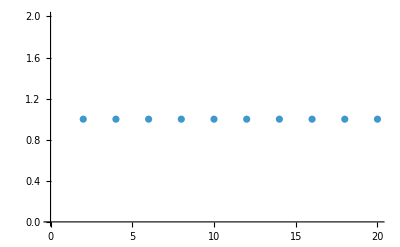

```mathematica
ListPlot[Table[{J,(Abs[N[exprJ[J,10]]/IPt[J,10 ]])},{J,2,20,2}]]
```

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Full divergent part part

```mathematica
Clear[exprJkeyhole,exprJthresh]
exprJkeyhole[J_,s_,n_]:=Module[{div,divT,exprSTU,expr,DiscExprT,exprJmain,exprJkeyhole1},
div[ss_]:=(4-ss)^-n;
divT[ss_]:=(-1)^n(ss-4)^-n;
exprSTU[ss_,t_,u_]:=div[ss]+div[u]+div[t];
expr[ss_,z_]:=exprSTU[ss, tt[ss,z],uu[ss,z]];
DiscExprT[ss_,z_]:=divT[tt[ss,z]];
exprJmain[JJ_,ss_]:=MyNIntegrateFaster[(PolQ[JJ,d,z]DiscExprT[ss,z])//CompactIntegrand[#,z,z0t[ss]+Exp[I Arg[-1+z0t[ss]]] 10^-5]&,{ϕ,0,π},p0];
exprJkeyhole1[JJ_, ss_, ord_: 4] := Module[
	  {z0, dir, eps, α, c0, qk},
	  z0  = z0t[ss];
	  dir = Exp[I Arg[z0 - 1]];   (* direction of the cut / keyhole ray *)
	  eps = 10^-5;
	  α   = n ;
	  (* regular prefactor of the discontinuity at the branch point *)
	  c0 = Limit[(z - z0)^α DiscExprT[ss, z],z -> z0,Direction -> dir];
	  qk[k_] := SeriesCoefficient[PolQ[JJ, d, z], {z, z0, k}];
	  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
	];
exprJmain[J,s]+exprJkeyhole1[J,s]
];
exprJthresh[J_,s_]:=Module[{Residue, Keyhole},
Residue=Sum[α[0,0,0,Boole[EvenQ[d]]-2(n-Floor[(d-3)/2])](Pi (-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0t[s])((s-4)/2)^-n,{n,Floor[(d-3)/2],1,-1}];
Keyhole=Sum[α[0,0,0,Boole[OddQ[d]]-2(n-Floor[(d-4)/2]-1/2)]exprJkeyhole[J,s,n],{n,Floor[(d-4)/2]+1/2,1/2,-1}];
Residue+Keyhole/.mysdpbout[[2]]
];
```

```mathematica
exprJthresh[3,10+I]
```

0.0035709538+0.0038488178 ⅈ